### A Quick Review of Electrostatics

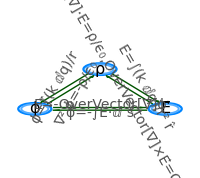

```mathematica
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
colors={RGBColor[0, 0.52, 1],RGBColor[Rational[1, 3], 0.6799999999999999, 1],GrayLevel[0.32],RGBColor[0, 0.33, 0]};
θ1=π/2;θ2=π/2+2π/3;θ3=π/2+4π/3;
p1={Cos[θ1],Sin[θ1]};p2={Cos[θ2],Sin[θ2]};p3={Cos[θ3],Sin[θ3]};
ft2=Style[#,14,FontFamily->"Times New Roman"]&;
s2=0.17;s3=0.9;
centerPlot@Graphics[{{colors[[1]],Thickness[0.008],Circle[#,0.22]&/@{p1,p2,p3}},{colors[[2]],Thickness[0.007],Circle[#,0.18]&/@{p1,p2,p3}},Text[font["ρ",16],p1],Text[font["ϕ",16],p2],Text[font["E⃗",16],p3],{colors[[4]],Arrow[1.1{{p1+s2(p2-p1),p2-s2(p2-p1)},{p3+s2(p2-p3),p2-s2(p2-p3)},{p1+s2(p3-p1),p3-s2(p3-p1)}}],Arrow[0.9{{p1+s3(p2-p1),p2-s3(p2-p1)},{p3+s3(p2-p3),p2-s3(p2-p3)},{p1+s3(p3-p1),p3-s3(p3-p1)}}]},Text[font["E⃗=-OverVector[∇]ϕ",colors[[3]]],(p2+p3)/2+{0,0.15}],Text[font["ϕ=-∫E⃗·ⅆ s⃗",colors[[3]]],(p2+p3)/2-{0,0.17}],Text[Rotate[font["∇^2 ϕ=-ρ/ϵ_0",colors[[3]]],Pi/3],(p1+p2)/2+{0.13,-0.18}],Text[Rotate[font["ϕ=∫(k ⅆq)/r",colors[[3]]],Pi/3],(p1+p2)/2+{-0.166,0.062}],Text[Rotate[font["E⃗=∫(k ⅆq)/r^2 r̂",colors[[3]]],-Pi/3],(p1+p3)/2+{0.172,0.09}],Text[Rotate[font["OverVector[∇]·E⃗=ρ/ϵ_0,OverVector[∇]×E⃗=OverVector[0]",colors[[3]]],-Pi/3],(p1+p3)/2+{-0.126,-0.15}]},ImageSize->200]
```

It is important to realize that although we have been focusing specific charge distributions from points, lines, sheets, and spheres, electricity is one of the most prevalent and influential forces that we encounter in our daily lives! This remarkable YouTube video highlights some amazing electricity tricks that you can easily test out for yourself!

### Normal Track

#### The Slab

What is the electric field everywhere due to a slab (an infinite sheet with thickness d with uniform charge density ρ)? Verify your answer in multiple ways.

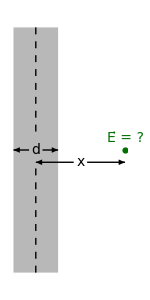

```mathematica
s=0.3;
centerPlot@Graphics[{{GrayLevel[0.72],Rectangle[{0,-5},{2,5}]},Arrowheads[0.05],Text[font["d",Italic],{1,0}],Text[font["x",Italic],{3,-0.5}],{Darker@Darker@Green,PointSize[0.03],Point[{5,0}],Text[font@"E⃗ = ?",{5,0.5}]},Arrow[{{{1-s,0},{0,0}},{{1+s,0},{2,0}}}],Arrow[{{{3-s,-0.5},{1,-0.5}},{{3+s,-0.5},{5,-0.5}}}],Dashed,Line[{{{1,-5},{1,-0.5}},{{1,5},{1,0.5}}}]},ImageSize->150]
```

Solution
We can solve this setup in multiple ways using all of the tools that we have developed! In all cases, we start by using symmetry to note that the electric field E⃗=E[x]x̂ must point in the x̂ direction and cannot depend upon y or z.

Method 1: Use Coulomb's Law on the Slab (Cartesian coordinates)
This method is straightforward, but computationally cumbersome. Nevertheless, we can integrate over the entire slab (and only taking the x-component of the electric field). Since the electric field is independent of y and z, let’s compute the field at the point (x,0,0). We will consider the contribution from the little chunk of the slab at position (x̃,ỹ,z̃) with volume ⅆ x̃ⅆ ỹⅆ z̃. The horizontal component of the electric field contribution from this small chunk is Cos[θ]=(x-x̃)/(((x-x̃)^2+(ỹ)^2+(z̃)^2)^(1/2)). Therefore, the total electric field is given by the following integral (which is best to evaluate using Mathematica)

(E⃗)_slab=x̂∫(k ⅆq)/r^2 Cos[θ]=x̂∫_(-d/2)^(d/2) ∫_(-∞)^∞ ∫_(-∞)^∞ (k (ρ ⅆ x̃ⅆ ỹⅆ z̃))/((x-x̃)^2+(ỹ)^2+(z̃)^2)=Piecewise[{{(ρ d)/(2 ϵ_0) x̂, d/2<x}, {(ρ x)/ϵ_0 x̂, -d/2<x<d/2}, {-(ρ d)/(2 ϵ_0) x̂, x<-d/2}}]

```mathematica
(* Evaluate E⃗ for 0<x and use symmetry to determine E⃗ for x<0 *)
Integrate[(k ρ(x-xx))/(((x-xx)^2+yy^2+zz^2)^(3/2)),{xx,-d/2,d/2},{yy,-∞,∞},{zz,-∞,∞},Assumptions->0<d<x]/.k->1/(4π ϵ0)
Integrate[(k ρ(x-xx))/(((x-xx)^2+yy^2+zz^2)^(3/2)),{xx,-d/2,d/2},{yy,-∞,∞},{zz,-∞,∞},Assumptions->0<x<d/2]/.k->1/(4π ϵ0)
```

(d ρ)/(2 ϵ0)

(x ρ)/ϵ0

Method 2: Use Gauss’s Law
In any case where there is enough symmetry to apply Gauss’s Law, it will always be the simplest way to compute the electric field. In this case, since we know that E⃗=E[x]x̂, we can consider a Gaussian cylinder of length 2x with its symmetry axis along the x-axis, and whose faces have area A and lie at x and -x (and therefore symmetrically split the y-z plane). The integral ∫E⃗·ⅆ a⃗ will be zero along the curved surface of the Gaussian cylinder (since ⅆ a⃗ never points in the x-direction while E⃗ does), whereas E⃗ and ⅆ a⃗ point in the same direction on the faces of the cylinder, so ∫E⃗·ⅆ a⃗=∫_faces E[x]ⅆa=E[x]∫_faces ⅆa where we have used the face that E[x]=E[-x] has the same magnitude on both faces of the cylinder to pull it out of the integral.

We are now ready to use Gauss’s Law. However, we need to be careful to define whether the length 2x of the cylinder is larger or smaller than the width d of the slab. If d/2<x, then the cylinder spans the entire slab and we obtain

∫E⃗·ⅆ a⃗=Q_enc/ϵ_0

E[x]∫_faces ⅆa=(ρ A d)/ϵ_0

E[x](2A)=(ρ A d)/ϵ_0

E⃗=(ρ d)/(2 ϵ_0)x̂     (d/2<x)

If 0<x<d/2, the cylinder only contains part of the slab, so Q_enc will be smaller,

∫E⃗·ⅆ a⃗=Q_enc/ϵ_0

E[x]∫_faces ⅆa=(ρ A (2x))/ϵ_0

E[x](2A)=(ρ A (2x))/ϵ_0

E⃗[x]=(ρ x)/ϵ_0 x̂     (0<x<d/2)

Combining these two results and using the fact that E⃗[-x]=-E⃗[x], we find the same result as in Equation (TextNumbered).

Method 3: Use the Principle of Superposition and Analyze the Slab as Multiple Thin Sheets
An equally simple way to analyze the slab is to consider it as an assembly of multiple thin sheets. The thin sheet at position x with width ⅆx has an effective surface charge σ=ρⅆx, and hence creates the general electric field σ/(2 ϵ_0) pointing away from itself.

For points outside the sheet (further than d/2 on the x-axis), the electric field of all sheets will combine in the same direction, yielding the net field

E⃗=x̂∫σ/(2 ϵ_0)=x̂∫_(-d/2)^(d/2) ρⅆx/(2 ϵ_0)=(ρ d)/(2 ϵ_0)x̂

For points inside the sheet (at an x between 0 and d/2 on the x-axis), there will be partial cancelation of the electric field,

E⃗=x̂∫_(-d/2)^x ρⅆx/(2 ϵ_0)-x̂∫_x^(d/2) ρⅆx/(2 ϵ_0)=((ρ (x+d/2))/(2 ϵ_0)-(ρ (d/2-x))/(2 ϵ_0))x̂=(ρ x)/ϵ_0 x̂

as found above. □

#### Inner-Surface Charge Density

A positive point charge q is located off-center inside a neutral conducting spherical shell. We know from Gauss’s law that the total charge on the inner surface of the shell is -q. Is the surface charge density negative over the entire inner surface? Or can it be positive on the far side of the inner surface if the point charge q is close enough to the shell so that it attracts enough negative charge to the near side? Justify your answer. 
Hint: Think about field lines.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
If there were a location with positive density, then electric field lines would start there, pointing away from it into the spherical cavity. But where could these field lines end? They can’t end at infinity, because that’s outside the shell. And they can’t end at a point in empty space, because that would violate Gauss’s law; there would be nonzero flux into a region that contains no charge. They also can’t end on the positive point charge q, because the field lines point outward from q. And finally they can’t end on the shell, because that would imply a nonzero line integral of E⃗ (and hence a nonzero potential difference) between two points on the shell. But we know that all points on the conducting shell are at the same potential. Therefore, such a field line (pointing inward from the inner surface) can’t exist. So all of the inner surface charge must be negative. Every field line inside the cavity starts at the point charge q and ends on the shell. □

#### Triangular E

Find the charge density ρ and potential φ associated with the electric field shown in the figure below. E is independent of y and z. Assume that φ=0 at x=0.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
Since E is independent of y and z, we should integrate ϕ=-∫E⃗[x]·ⅆs along the x-axis. Note that because the charge distribution goes out to infinity, we don’t set the zero potential at infinity (which would not be well defined), but instead use x=0. At a distance 0<x<a,

ϕ=-∫_0^x E[x̃]ⅆ x̃=-∫_0^x E_0(1-(x̃)/a)ⅆ x̃=-(E_0(x̃-(x̃)^2/(2a)))_(x̃=0)^(x̃=x)=E_0(x^2/(2a)-x)

For distances x>a, note that E[x]=0 for x>a so that ϕ[x]=ϕ[a] for this range. For x<0, we do a similar calculation to Equation (TextNumbered) above,

ϕ=-∫_0^x E[x̃]ⅆ x̃=-∫_0^x E_0(1+(x̃)/a)ⅆ x̃=-(E_0(x̃+(x̃)^2/(2a)))_(x̃=0)^(x̃=x)=-E_0(x^2/(2a)+x)

In summary,

ϕ=Piecewise[{{(E_0 a)/2, x<-a}, {-E_0(x^2/(2a)+x), -a≤x<0}, {E_0(x^2/(2a)-x), 0≤x<a}, {-(E_0 a)/2, a≤x}}]

The charge density ρ=-ϵ_0OverVector[∇]·E⃗=-(∂E)/(∂x). This is just a straightforward derivative which equals

ρ=Piecewise[{{0, x<-a}, {(ϵ_0 E_0)/a, -a≤x<0}, {-(ϵ_0 E_0)/a, 0≤x<a}, {0, a≤x}}]

This form of ρ shows us that the charge distribution is two infinity slabs with thickness a and opposite charge densities ±(ϵ_0 E_0)/a that touch at the x=0 plane (these are the same constructs considered in the first question in the Normal Track). With this, we have a complete picture of the setup.

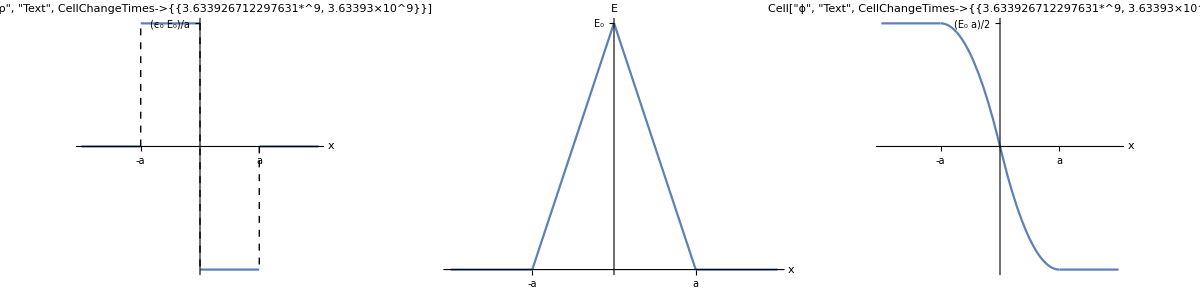

```mathematica
ρPlot=Show[Plot[{Piecewise[{{0,x<-1},{1,-1<x<0},{-1,0<x<1},{0,1<x}}]},{x,-2,2},Ticks->{{{1,"a"},{-1,"-a"}},{{1,"(ϵ_0 E_0)/a"}}},ImageSize->200,AxesLabel->{"x","Cell["ρ", "Text",CellChangeTimes->{{3.633926712297631*^9, 3.63393×10^9}},ExpressionUUID->"b18e0a51-c552-449e-bef2-6fe83189ea5d"]"}],Graphics[{Dashed,Line[{{-1,0},{-1,1}}],Line[{{0,1},{0,-1}}],Line[{{1,0},{1,-1}}]}]];
EPlot=Plot[{Piecewise[{{0,x<-1},{1+x,-1<x<0},{1-x,0<x<1},{0,1<x}}]},{x,-2,2},Ticks->{{{1,"a"},{-1,"-a"}},{{1,"E_0"}}},ImageSize->200,AxesLabel->{"x","E"}];
ϕPlot=Plot[{Piecewise[{{1/2,x<-1},{-x^2/2-x,-1<x<0},{x^2/2-x,0<x<1},{-1/2,1<x}}]},{x,-2,2},Ticks->{{{1,"a"},{-1,"-a"}},{{1/2,"(E_0 a)/2"}}},ImageSize->200,AxesLabel->{"x","Cell["ϕ", "Text",CellChangeTimes->{{3.633926712297631*^9, 3.63393×10^9}},ExpressionUUID->"430748d7-2411-474b-981e-2a1a3ad0e8a4"]"}];
centerPlot@Grid[{{ρPlot,EPlot,ϕPlot}}]
```

As a double check, at x=0 the two infinite slabs act effectively like sheets with charge densities ±σ=±ρ a. They create a field pointing to the right with magnitude σ/(2 ϵ_0), so the total field is 2(ρ a)/(2 ϵ_0)=(ρ a)/ϵ_0. Since we found that ρ=(ϵ_0 E_0)/a, the field equals E_0, in agreement with the given value. □

### Hard Track

#### Two Concentric Shells

The shaded regions in the figure below represent two neutral concentric conducting spherical shells. The white regions represent vacuum. Two point charges q are located as shown; the interior one is off-center.

Draw a reasonably accurate picture of the field lines everywhere, and indicate the various charge densities. What quantities are spherically symmetric? 
(As discussed in Exercise 3.49, there are two possible cases for what your picture can look like, depending on how close the exterior point charge is; take your pick.)

Repeat the above tasks in the case where the two shells are connected by a wire, so that they are at the same potential.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
The charge distribution and field lines are shown (roughly) below. Let the surfaces be labeled 1, 2, 3, and 4 starting from the innermost one. There is charge -q on surface 1. This is true because the field is zero inside the metal of the conductor, so a spherical Gaussian surface drawn inside the metal of the inner conductor has no flux, and hence the net charge enclosed in the sphere must be zero. The negative surface charge density on surface 1 is higher near the off-center point charge. Since the inner conductor is neutral, a charge +q must reside on surface 2. This surface charge density is spherically symmetric, because it feels no field from the charges inside (or outside) of it, due to the zero field inside the metal of the conductors.)

```mathematica
centerPlot@-Graphics-
```

-Graphics-

By the same Gauss’s law reasoning, there must be a charge -q on surface 3, because there is zero field inside the metal of the outer conductor. The surface charge density is spherically symmetric. A charge +q is left for surface 4. This surface charge density is actually negative near the outer charge q if that charge is located close enough to the shells (see Exercise 3.49 for more details). But in any case, the total charge on surface 4 is +q. Between the shells, the field is spherically symmetric, consistent with the spherically symmetric charge densities on surfaces 2 and 3.

For the second part of the problem, the shells are now at the same potential, so the field between them must be zero. Therefore, the only difference from the scenario in Part a is that we just need to erase the field between the shells and erase the charges on surfaces 2 and 3. The charges on surfaces 1 and 4 aren’t effected by this change, because the surfaces 2 and 3 together produced zero field everywhere except between them. □

#### Two Slightly-Offset Nonconducting Spheres

Two spheres, each of radius R and carrying uniform charge densities +ρ and -ρ, are placed so that they partially overlap. (Assume they can somehow freely pass through each other.) Show that the electric field everywhere in the region of overlap between the two spheres is constant and determine its magnitude and direction.

```mathematica
centerPlot@Graphics3D[{Opacity[0.2],{Blue,Sphere[]},{Red,Sphere[{0.9,0,0}]}},ViewPoint->{0,-3.4,0},Boxed->False,ImageSize->250]
```

-Graphics3D-

Solution
Define the vector from the center of the positively charged sphere to the center of the negatively charged sphere to be d⃗ as shown below. For any point in the region of intersection between the two spheres, let (r⃗)_1 and (r⃗)_2 be the vectors from the centers of the spheres with positive and negative charge to the point, respectively.

```mathematica
pt1={0,0,0};pt2={1.4,0,0};pt3={0.6,0,0.25};
centerPlot@Graphics3D[{{Opacity[0.2],{Blue,Sphere[pt1]},{Red,Sphere[pt2]}},Point[pt3],Arrow[{{pt1,pt2},{pt1,pt3},{pt2,pt3}}],Text[font@"d⃗",Mean[{pt1,pt2}]+{0,0,-0.17}],Text[font@"(r⃗)_1",Mean[{pt1,pt3}]+{-0.05,0,0.15}],Text[font@"(r⃗)_2",Mean[{pt2,pt3}]+{0.05,0,0.15}]},ViewPoint->{0,-3.4,0},Boxed->False,ImageSize->250]
```

-Graphics3D-

Recall that the electric field of a uniformly charged solid sphere with charge density ρ is given by E⃗=(ρ r)/(3 ϵ_0)r̂ (as can be quickly verified using Gauss’s Law) where r is the distance from the point to the center of the sphere and r̂ is the unit vector pointing radially away from the sphere’s center. Using r r̂=r⃗, we can rewrite this expression as E⃗=ρ/(3 ϵ_0)r⃗. Using the notation from the figure above, the electric field at any point in the intersecting region will be

E⃗=ρ/(3 ϵ_0)(r⃗)_1-ρ/(3 ϵ_0)(r⃗)_2=ρ/(3 ϵ_0)d⃗

where we have used the definition d⃗=(r⃗)_1-(r⃗)_2. Therefore, the electric field in the region of intersection is uniform with magnitude (ρ d)/(3 ϵ_0) pointing in the direction from the positive to the negatively charged sphere. □

#### Concurrent Field Lines

A semicircular wire with radius R has uniform charge density −λ. Show that at all points along the “axis” of the semicircle (the line through the center, perpendicular to the plane of the semicircle, as shown in the following figure), the vectors of the electric field all point toward a common point in the plane of the semicircle. Where is this point?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
Assume that the "axis" of the semicircle lies along the y-axis. By symmetry, the x-component of the electric field equals zero. We will consider the electric field at the point (0,0,z).

If we parameterize the semicircle by an angle θ going from 0 to π, then the bit of charge λ R ⅆθ will create an electric field with magnitude (k (λ Rⅆθ))/(R^2+z^2) at the point (0,0,z). What is the component of this electric field in the y-direction and z-direction? Since the charge lies at (R Cos[θ],R Sin[θ],0), the vector from the point (0,0,z) to this charge (points in the same direction as the electric field contribution from this charge) equals ⟨R Cos[θ],R Sin[θ],-z⟩. So the component in the y-direction and z-direction equals the magnitude of the electric field multiplied by (R Sin[θ])/(√(R^2+z^2)) and -z/(√(R^2+z^2)), respectively. Therefore, the electric field in the y-direction and z-direction equals

E_y=∫_0^π (k (λ Rⅆθ))/(R^2+z^2)(R Sin[θ])/((R^2+z^2)^(1/2))=(2k R^2 λ)/((R^2+z^2)^(3/2))

E_z=∫_0^π (k (λ Rⅆθ))/(R^2+z^2)-z/((R^2+z^2)^(1/2))=-(k π R z λ)/((R^2+z^2)^(3/2))

(You should also setup and carry out the integration for E_x and prove that it is zero algebraically, even though we know that it must be so geometrically.)

Therefore, the electric field line passes through the point (0,0,z) with E_z/E_y=-z/((2 R)/π). When this line moves down along the z-axis by z it moves up along the y-axis by (2R)/π, so that all of the lines merge at the point (0,(2R)/π,0). Note that this point is independent of z, as desired.

This point also happens to be the "center of charge" of the semi-circle, or equivalently, the center of mass of a semicircle with a uniform mass density (which by symmetry lies on the y-axis at the point y_cm=(∫y ⅆm)/(∫ⅆm)=(∫_0^π (R Sin[θ])(λ R ⅆθ))/(∫_0^π λ R ⅆθ)=(2 R^2 λ)/(π R λ)=(2R)/π). This result is consistent with the following intuitive fact (which you can easily prove for yourself): far away from a distribution of charges, the electric field points approximately towards the center of the charge of the distribution. For nearby points, it generally doesn’t, although it happens to (exactly) point in that direction for points on the axis of the present setup. □

### Insane Track

#### Zero Field in a Sphere

A sphere with radius R is centered at the origin, an infinite cylinder with radius R has its axis along the z-axis, and an infinite slab with thickness 2R lies between the planes z=−R and z=R. The uniform volume densities of these objects are ρ_1, ρ_2, and ρ_3, respectively. The objects are superposed on top of each other; the densities add where the objects overlap. How should the three densities be related so that the electric field is zero everywhere throughout the volume of the sphere? 
Hint: Find a vector expression for the field inside each object, and then use superposition.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
First, we need to compute the electric field from the slab, cylinder, and sphere at a point (x,y,z) inside the sphere - the simplest way to proceed is using Gauss’s Law. The electric field from the slab (see the first problem in the Normal Track) is given by

(E⃗)_slab=(ρ_3 z)/ϵ_0 ẑ=ρ_3/ϵ_0 z⃗

where z⃗=⟨0,0,z⟩. The computation for the cylinder proceeds similarly, yielding

(E⃗)_cylinder=(ρ_2 r_cyl)/(2 ϵ_0) (r̂)_cyl=ρ_2/(2 ϵ_0) (r⃗)_cyl

where (r⃗)_cyl=⟨x,y,0⟩ is the cylindrical coordinate representing the distance from the z-axis. Finally, the electric field from the sphere equals

(E⃗)_sphere=(ρ_1 r_sph)/(3 ϵ_0) (r̂)_sph=ρ_1/(3 ϵ_0) (r⃗)_sph

where this time (r⃗)_sph=⟨x,y,z⟩ is the spherical coordinate distance from the origin. Notice that (r⃗)_sph=(r⃗)_cyl+z⃗. Therefore, the electric field inside the sphere equals zero provided that

(E⃗)_slab+(E⃗)_cylinder+(E⃗)_sphere= OverVector[0]

ρ_3/ϵ_0 z⃗+ρ_2/(2 ϵ_0) (r⃗)_cyl+ρ_1/(3 ϵ_0) (r⃗)_sph= OverVector[0]

ρ_3/ϵ_0 z⃗+ρ_2/(2 ϵ_0) (r⃗)_cyl+ρ_1/(3 ϵ_0)((r⃗)_cyl+z⃗)= OverVector[0]

(ρ_3/ϵ_0+ρ_1/(3 ϵ_0))z⃗+(ρ_2/(2 ϵ_0)+ρ_1/(3 ϵ_0)) (r⃗)_cyl= OverVector[0]

Since z⃗ and (r⃗)_cyl point orthogonally to each other, their sum can only be zero if both terms in parentheses are zero, and hence

ρ_1=-3 ρ_3

ρ_2=2 ρ_3

As a double check, the sum of these three densities (which is the net density inside the sphere) equals zero. This is correct, because if the field inside the sphere is zero, then any volume we choose inside the sphere must contain zero charge, since there is zero flux through its surface. The only way this can happen is if there is no charge anywhere inside the sphere. Hence ρ=0. This is consistent with the differential form of Gauss’s Law, OverVector[∇]·E⃗=ρ/ϵ_0, since E⃗=OverVector[0] implies ρ=0. □

#### Zero Flow

Two spheres, of radii R_1 and R_2, are held so far apart from one another that each one negligibly feels the electric field from the other sphere. We want to divide a total amount of charge Q between the two spheres (assume both are conductors, so that the charge will be distributed evenly on each sphere).

How should the charge Q be split between the two spheres to make the potential energy of the resulting charge distribution as small as possible? Given this allocation of charge, what is the potential at the surface of both spheres? Justify this result.

If R_1≠R_2, the amount of charge on the two spheres will not be the same. If we connect the spheres with a thin conducting wire, will charge flow between them? Your answer may appear a bit strange, because the electric field is proportional to 1/r^2, so the field is much larger at the surface of the smaller sphere than the larger sphere, because the charge is proportional only to r. So why doesn’t the charge get repelled from the smaller sphere and ﬂow through the wire to the larger sphere? 
Hint: Assume that only a tiny bit of charge flows onto this wire, and that this charge is uniformly distributed to make a charge density λ. What is the total force on this wire?

Solution
For the first part of the problem, assume charge Q_1 is spread over the sphere with radius R_1, leaving charge Q−Q_1 to be spread onto the other sphere with radius R_2. Since the two spheres are held sufficiently far apart that they effectively cannot sense one another’s electric field, the energy of the sphere with radius R_1 is given by

U_(R_1 sphere)=1/2∫ρ ϕ ⅆv=1/2 Q_1 ((k Q_1)/R_1)=(k Q_1^2)/(2 R_1)

and the energy of the second sphere is similarly U_(R_2 sphere)=(k (Q-Q_1)^2)/(2 R_2). To minimize the total energy, we differentiate U_tot=U_(R_1 sphere)+U_(R_2 sphere) with respect to Q_1,

0=(ⅆ U_tot)/(ⅆ Q_1)=(k Q_1)/R_1-(k (Q-Q_1))/R_2

which yields

Q_1=R_1/(R_1+R_2)Q

The potential on the surface of the R_1 sphere will therefore be (k Q_1)/R_1=k Q R_1/(R_1+R_2) while the potential on the surface of the R_2 sphere will be (k Q_2)/R_2=k Q R_2/(R_1+R_2), so the potential difference between the two spheres is zero. This had to be the case, since otherwise we could have taken a bit of charge from the sphere with more potential at its surface, moved that charge to the other sphere, and decreased the total energy of the system, contradicting the notion that the system has achieved its minimum energy.

For the second part of the problem, note that if the two spheres were connected by a wire, then no charge would flow between them (since their surface are at the same potential). As the problem states, this seems rather odd, so let’s justify it quantitatively. Assuming that the thin wire has constant charge density λ, the total force on it due to the sphere of radius R_1 equals

∫_R_1^∞ (k Q_1)/r^2(λ ⅆr)=(k λ Q_1)/R_1=(k λ Q)/(R_1+R_2)

where we have placed the upper bound at infinity because we assumed that the two spheres are very far apart (more accurately, the integral would be ∫_R_1^(D-R_2) (k λ Q_1)/r^2 ⅆr where D is the distance between the centers of the sphere, but by making D large enough we can make the correction term between this integral and our integral negligible). Similarly, the force due to the second sphere equals

∫_R_2^∞ (k Q_2)/r^2(λ ⅆr)=(k λ Q_2)/R_2=(k λ Q)/(R_1+R_2)

Therefore, the force on the wire is equal, and the charges won’t move between them. Note that although the force on the surface of the smaller sphere is greater, the force from the smaller sphere also dies off much faster than that of the larger sphere. The full integrals shows that they are ultimately equivalent, and this is also shown by the graph below.

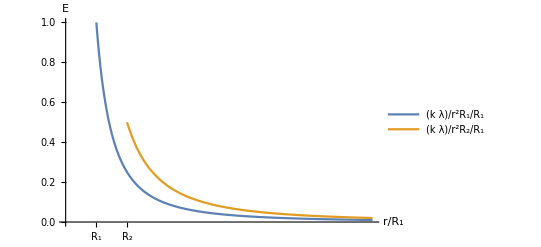

```mathematica
centerPlot@Show[Plot[{1/r^2,-1},{r,1,10},PlotRange->{{0,10},{0,1}},AxesOrigin->{0,0},AxesLabel->(font[#,14]&/@{"r/R_1","E"}),PlotLegends->Placed[(font[#,16]&/@{"(k λ)/r^2R_1/R_1","(k λ)/r^2R_2/R_1"}),Scaled[{{0.78,0.65},{0.5,0.5}}]],Ticks->{{{1,font["R_1",14]},{2,font["R_2",14]}},None}],Plot[{2/r^2},{r,2,10},PlotStyle->ColorData[97][2],PlotRange->{{0,10},{0,1}},AxesOrigin->{0,0}]]
```

So only a very tiny bit of charge goes onto the wire, and all the remaining charge will stay on the two spheres. The only remaining point is to discuss our initial assumptions: that only a tiny bit of charge goes onto the wire and that this charge is uniformly distributed along the wire. The first point is discussed in Problem 3.10 where it is shown that a thin wire has essentially zero capacitance. The second point is discussed in Problem 3.5, which is definitely worth a read! □

#### Field from a Cylindrical Shell, Right and Wrong

Find the electric field outside a uniformly charged hollow cylindrical shell with radius R and charge density σ, an infinitesimal distance away from it. Do this in the following two ways:

1. Slice the shell into parallel infinite rods, and integrate the field contributions from all the rods. You should obtain the incorrect result of σ/(2 ϵ_0).

2. Why isn't the result correct? Explain how to modify it to obtain the correct result of σ/ϵ_0. 
Hint: You could very well have performed the above integral in an effort to obtain the electric field an infinitesimal distance inside the cylinder, where we know the field is zero. Does the above integration provide a good description of what's going on for points on the shell that are very close to the point in question?

3. Confirm that the result equals σ/ϵ_0 by straight up integration assuming that the point is a finite distance z away from the center of the cylinder. What happens when z<R, z=R, and z>R?

Solution
1. Let the rods be parameterized by the angle θ as shown in the diagram below.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

The width of a rod is R ⅆθ, so its effective charge per unit length is λ=σ (Rⅆθ). The rod is a distance 2R Sin[θ/2] from the point P in question, which is infinitesimally close to the top of the cylinder. Only the vertical component of the field from the rod survives, and this brings in a factor of Sin[θ/2]. Using the fact that the field from a rod is λ/(2π ϵ_0 r), we find that the field at the top of the cylinder is (incorrectly)

2∫_0^π (σ R ⅆθ)/(2π ϵ_0(2R Sin[θ/2]))Sin[θ/2]=σ/(2π ϵ_0)∫_0^π ⅆθ=σ/(2 ϵ_0)

Interestingly, we see that for a given angular width of a rod, all rods yield the same contribution to the vertical electric field at P (since the ones further away from it contribute at a better angle).

2. As stated in the problem, it is no surprise that this answer is incorrect, since the same calculation would supposedly yield the field just inside the cylinder too, where it is zero instead of σ/ϵ_0. However, this calculation does yield the average of these two values.

The reason why the calculation is invalid is that it doesn’t correctly describe the field due to rods very close to the given point, that is, for rods with θ≈0. It is incorrect for two reasons. First, the distance from a rod to the given point is not equal to 2R Sin[θ/2]. Additionally, the field does not point along the line from the rod to the top of the cylinder. It points more vertically, so the extra factor of Sin[θ/2] which we used to pick out the vertical component isn’t valid.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

What is true is that if we remove a thin strip from θ=-ϕ/2 to θ=ϕ/2 (for very small ϕ≪1) at the top of the cylinder, then the above integral is valid for the remaining part of the cylinder. In other words, the electric field due to the remaining cylinder will be (2π-ϕ)/(2π)σ/(2 ϵ_0)≈σ/(2 ϵ_0) since we can make (2π-ϕ)/(2π) arbitrarily close to 1. By superposition, the total field of the entire cylinder in this field of σ/(2 ϵ_0) plus the field due to the thin strip at the top. But if the point in question is infinitesimally close to the cylinder, then the thin strip will look like an infinite plane, the field of which we know is σ/(2 ϵ_0). The desired total field is then

E_outside=E_(cylinder minus strip)+E_strip=σ/(2 ϵ_0)+σ/(2 ϵ_0)=σ/ϵ_0

E_inside=E_(cylinder minus strip)-E_strip=σ/(2 ϵ_0)-σ/(2 ϵ_0)=0

where the minus sign in E_inside comes from the fact that E_strip (like an infinite sheet) points in different directions inside and outside the cylinder.

Technical note: We have two infinitesimally small quantities in this problem: the width ϕ of the strip that we are removing from the cylinder and the infinitesimal distance of the point P from the cylinder. You may (or at least should) be wondering which of these two infinitesimally small quantities is smaller. This is an important point to keep track of - if you are blasé about the matter and simply send both quantities to 0 without regard, you could end up with wrong results! In this problem, we want for the distance from P to the cylinder to be smaller, and indeed that is the case. For we first picked a small ϕ (which we can make as small as we like) and then we considered a point P which was essentially touching the cylinder but on the outside; you can think of this as once you fix ϕ, you bring P in extremely close to the cylinder (and therefore extremely close to the thin strip).

3. Orient the cylinder’s axis to lie on the y-axis and consider the electric field at the point (0,0,z).

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Define the distance from the wire at angle θ to the point (0,0,z) to be r, which by the Law of Cosines equals r^2=R^2+z^2-2R z Cos[θ]. Using the charge density λ=σ (Rⅆθ), the electric field λ/(2π ϵ_0 r) from an infinite wire, and the z-component (z-R Cos[θ])/r of the electric field,

E=∫_0^(2π) (R σⅆθ)/(2π ϵ_0 r)(z-R Cos[θ])/r=(R σ)/(2π ϵ_0)∫_0^(2π) (z-R Cos[θ])/(R^2+z^2-2R z Cos[θ])ⅆθ

This integral is not super-difficult to evaluate, but care must be taken as to whether z<R, z=R, or z>R. The full result is given by

E=R/z(σ (1-Sign[R-z]))/(2 ϵ_0)

```mathematica
Integrate[(R σ)/(2π ϵ0)(z-R Cos[θ])/(R^2+z^2-2R z Cos[θ]),{θ,0,2π},Assumptions->0<ϵ0&&0<σ&&0<R&&0<z]
```

-(R σ (-1+Sign[R-z]))/(2 z ϵ0)

In other words,

E=Piecewise[{{0, z<R}, {σ/(2 ϵ_0), z=R}, {R/z σ/ϵ_0, z>R}}]

We see that when we approach the surface of the cylinder from the inside E=0, whereas when we approach it from the outside, E=R/z σ/ϵ_0→σ/ϵ_0. The electric field on the actual surface equals the average of these two values, E=σ/(2 ϵ_0). □

## Mathematica Initialization

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
RawBoxes@CounterBox["TextNumbered","eq1"]
```

TextNumbered